# Kelvin Problem in 2-d plane strain

```mathematica
x = xo - xs
y = yo - ys
C0 = 1/ (4 * Pi *(1-ν))
r = Sqrt[x^2 + y^2]
g = -C0 * Log[r]
gx = -C0*x/r^2
gy = -C0*y/r^2
ux = fx/(2*μ)*((3-4*ν)*g - x*gx) + fy/(2*μ)*(-y*gx) 
uy = fx/(2*μ)*(-x*gy) + fy/(2*μ)*((3-4*ν)*g -y*gy)
```

xo-xs

yo-ys

1/(4 π (1-ν))

√((xo-xs)^2+(yo-ys)^2)

-Log[√((xo-xs)^2+(yo-ys)^2)]/(4 π (1-ν))

-(xo-xs)/(4 π ((xo-xs)^2+(yo-ys)^2) (1-ν))

-(yo-ys)/(4 π ((xo-xs)^2+(yo-ys)^2) (1-ν))

-(fy (xo-xs) (-yo+ys))/(8 π ((xo-xs)^2+(yo-ys)^2) μ (1-ν))+(fx ((xo-xs)^2/(4 π ((xo-xs)^2+(yo-ys)^2) (1-ν))-((3-4 ν) Log[√((xo-xs)^2+(yo-ys)^2)])/(4 π (1-ν))))/(2 μ)

-(fx (-xo+xs) (yo-ys))/(8 π ((xo-xs)^2+(yo-ys)^2) μ (1-ν))+(fy ((yo-ys)^2/(4 π ((xo-xs)^2+(yo-ys)^2) (1-ν))-((3-4 ν) Log[√((xo-xs)^2+(yo-ys)^2)])/(4 π (1-ν))))/(2 μ)

```mathematica
uxmod = ReplaceAll[ux,{ys->0,yo->0}]
uymod = ReplaceAll[uy,{ys->0,yo->0}]
uxint = Integrate[uxmod,{xs,-1,1},Assumptions->{Im[xo]==0}]
uyint = Integrate[uymod,{xs,-1,1},Assumptions->{Im[xo]==0}]
```

(fx (1/(4 π (1-ν))-((3-4 ν) Log[√((xo-xs)^2)])/(4 π (1-ν))))/(2 μ)

-(fy (3-4 ν) Log[√((xo-xs)^2)])/(8 π μ (1-ν))

-(fx (2+1/2 (-3+4 ν) (-4-(-1+xo) Log[(-1+xo)^2]+(1+xo) Log[(1+xo)^2])))/(8 π μ (-1+ν))

(fy (-3+4 ν) (4-2 xo ArcTanh[(2 xo)/(1+xo^2)]+Log[1/((-1+xo^2)^2)]))/(16 π μ (-1+ν))

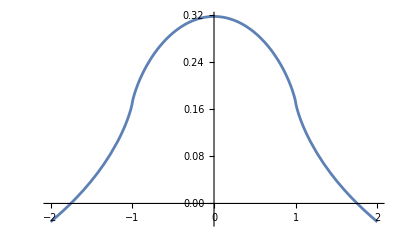

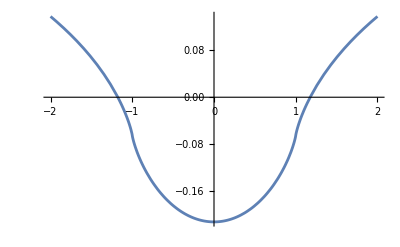

```mathematica
Plot[ ReplaceAll[uxint,{fx -> 1,fy->0, μ->1,ν->0.25}],{xo,-2,2}]
Plot[ ReplaceAll[uyint,{fx->0,fy -> -1, μ->1,ν->0.25}],{xo,-2,2}]
```

```mathematica
uxint2 = Integrate[Integrate[ux,{xs,-1,1},Assumptions->{Im[xo]==0}],ys, Assumptions->{Im[ys]==0}]
(*uxint2 = Integrate[ux,xs,ys]
uxdefint2 = ReplaceAll[uxint2, {xs->1,ys->0.1}] + ReplaceAll[uxint2, {xs->-1,ys->-0.1}] - ReplaceAll[uxint2, {xs->1,ys->-0.1}] - ReplaceAll[uxint2, {xs->-1,ys->0.1}]*)
```

$Aborted

```mathematica
Plot[ReplaceAll[uxdefint2,{fx -> 1,fy ->0,μ->1,ν->0.25,yo->0}],{xo,-2,2}]
ContourPlot[ReplaceAll[uxdefint2,{fx -> 1,fy ->0,μ->1,ν->0.25}],{xo,-2,2},{yo,-2,2}]
```